```mathematica
SolveNewton[f_,x0_,xtol_,ytol_,pmax_]:=
Module[{fderiv,xprev,x,p},
fderiv= f';
xprev=x0;
x=xprev-f[xprev]/fderiv[xprev];
p=1;
While[ Abs[xprev-x] ≥xtol && Abs[f[x]] ≥ytol&& p≤pmax,xprev=x;
x=xprev-f[xprev]/fderiv[xprev];
p+=1];
{x,p}]
```

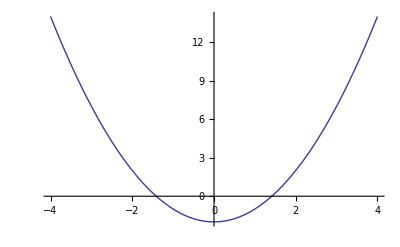

{1.41421,4}

```mathematica
f1[x_]:=x^2-2; Plot[f1[x],{x,-4,4}]
SolveNewton[f1,1.0,10^-6,10^-7,20]
```